```mathematica
file="/Users/vpk/Google\ Drive/Jlab/Projects/Mathematica/densities.txt";
Hdata=ReadList[file,{Number,Number,Number,Number,Number}];
X=Hdata[[All,1]];

HForwardu=Hdata[[All,2]];
HProfileu=Hdata[[All,3]];
HForwardd=Hdata[[All,4]];
HProfiled=Hdata[[All,5]];

xmin=1.9924×10^-5;
xmax=0.5;
ymin=0;
ymax=15;
HFu=Interpolation[Thread[{X,HForwardu}],InterpolationOrder->1];
HFd=Interpolation[Thread[{X,HForwardd}],InterpolationOrder->1];
HPu=Interpolation[Thread[{X,HProfileu}],InterpolationOrder->1];
HPd=Interpolation[Thread[{X,HProfiled}],InterpolationOrder->1];
Hu[x_,t_]:=HFu[x]*Exp[HPu[x]*t];
Hd[x_,t_]:=HFd[x]*Exp[HPd[x]*t];

PlotFL=Plot[{HFu[x],HFd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Forward Limit"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Forward Limit"];
PlotPF=Plot[{HPu[x],HPd[x]},{x,xmin,xmax},PlotRange->{{xmin,xmax},{ymin,ymax}},FrameLabel->{"x","Profile FUnction"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel->"Profile Function"];
xx=0.1;
 PlotH=Plot[{Hu[0.1,-t],Hd[0.1,-t]},{t,0,1},FrameLabel->{"-t","H(x=0.1,-t"},PlotLegends->Placed[{u-quark,d-quark},Center],Frame->True,Filling->Axis,ImageSize->Medium,PlotLabel-> "H(x=0.1,-t)"];
PlotHu=DensityPlot[Hu[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
PlotHd=DensityPlot[Hd[x,-t],{x,0.1,0.5},{t,0,1},ColorFunction->"SunsetColors",PlotLegends->Automatic];
Au=0.5;
Bu=0.5;
αu=0.3;
αu'=0.45;
nu=4.83;
βu=4;
ETPFu[x_]:=(Bu+αu'Log[1./x])*(1.-x)^3+Au*x*(1.-x)^2;
ETFLu[x_]:=nu*x^αu*(1.-x)^βu;


Ad=0.5;
Bd=0.5;
αd=0.3;
αd'=0.45;
nd=3.57;
βd=5;
ETPFd[x_]:=(Bd+αd'Log[1./x])*(1.-x)^3+Ad*x*(1.-x)^2;
ETFLd[x_]:=nd*x^αd*(1.-x)^βd;

ETu[x_,t_]:=ETFLu[x]*Exp[ETPFu[x]*t];
ETd[x_,t_]:=ETFLd[x]*Exp[ETPFd[x]*t];

GeVFm=0.1973;

HDeNu  [x_,bx_,by_]:=1./(4*π)*HFu[x]/HPu[x]*Exp[-(bx^2+by^2)/(4*HPu[x])];
ETDeNu[x_,bx_,by_]:=1./(4*π)*ETFLu[x]/ETPFu[x]*Exp[-(bx^2+by^2)/(4*ETPFu[x])];
DeNu    [x_,bx_,by_]:=1./2.*(HDeNu[x,bx,by]+1./4.*by/(0.938*ETFLu[x])*ETDeNu[x,bx,by]);
DenXYu[x_,bx_,by_]:=DeNu[x,bx/GeVFm,by/GeVFm]*GeVFm^2;

HDeNd  [x_,bx_,by_]:=1./(4*π)*HFd[x]/HPd[x]*Exp[-(bx^2+by^2)/(4*HPd[x])];
ETDeNd[x_,bx_,by_]:=1./(4*π)*ETFLd[x]/ETPFd[x]*Exp[-(bx^2+by^2)/(4*ETPFd[x])];
DeNd    [x_,bx_,by_]:=1./2.*(HDeNd[x,bx,by]+1./4.*by/(0.938*ETFLd[x])*ETDeNd[x,bx,by]);
DenXYd[x_,bx_,by_]:=DeNd[x,bx/GeVFm,by/GeVFm]*GeVFm^2;



xd=0.42;
(*Print["HFu",[xx],"=",HFu[xd]]
Print["HPu",[xd],"=",HPu[xd]]
Print["HDeNu[0.,0.]=",HDeNu[xd,0.,0.]]
Print["DenXYu[0.,0.]=",DenXYu[xd,0.,0.]]
Print["DenXYd[0.,0.]=",DenXYd[xd,0.,0.]]*)
```

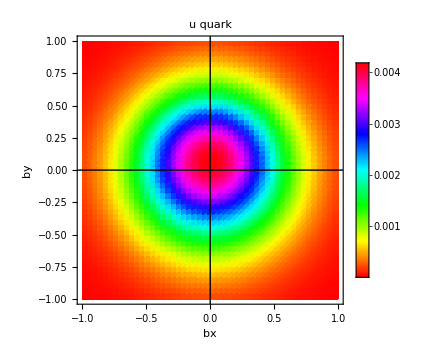
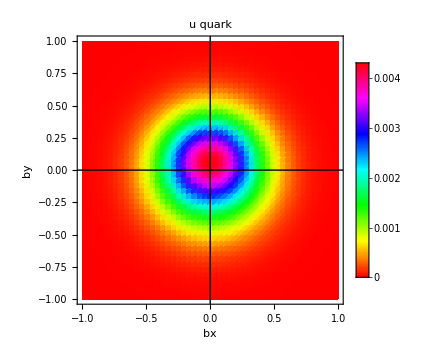
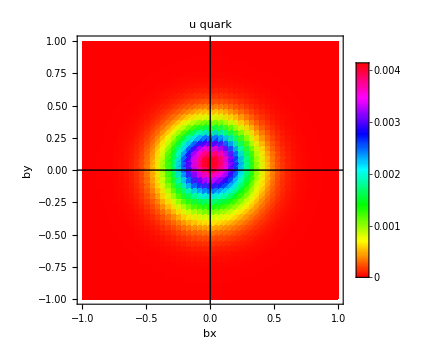
Grid[{-Graphics-,-Graphics-,-Graphics-}]

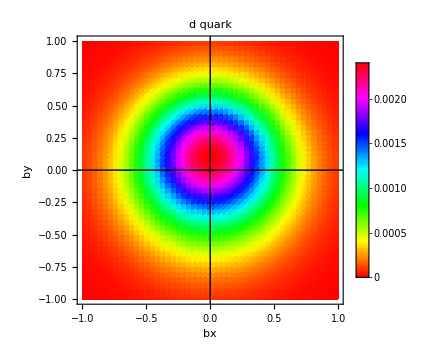
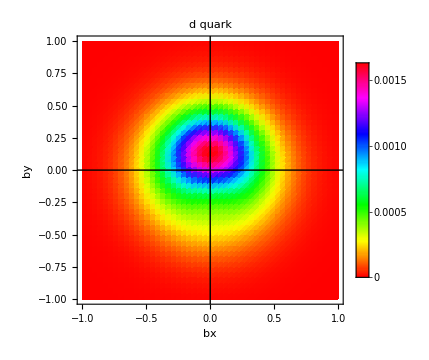
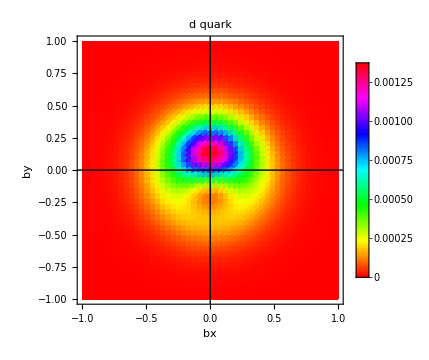
Grid[{-Graphics-,-Graphics-,-Graphics-}]

```mathematica
colfun="SunsetColors";
colfun=Hue;

plotGPDu[xz_]:=DensityPlot[DenXYu[xz,bx,by],{bx,-1,1},{by,-1,1},
PlotLabel->Style[StandardForm["u quark"],FontSize->25,FontColor->Black],
PlotLegends->Automatic, 
ColorFunction->colfun,
PlotPoints->50,
PlotRange->All,Axes->True,AxesLabel->{bx,by},
ImageSize->Medium,
Epilog->{Directive[{Thin,Black}],Line[{{-5,0},{5,0}}],Line[{{0,-5},{0,5}}]}];
plotGPDd[xz_]:=DensityPlot[DenXYd[xz,bx,by],{bx,-1,1},{by,-1,1},
PlotLabel->Style[StandardForm["d quark"],FontSize->25,FontColor->Black],
PlotLegends->Automatic, 
ColorFunction->colfun,
PlotPoints->50,
PlotRange->All,Axes->True,AxesLabel->{bx,by},
ImageSize->Medium,
Epilog->{Directive[{Thin,Black}],Line[{{-5,0},{5,0}}],Line[{{0,-5},{0,5}}]}];

Grid[{plotGPDu[0.1], plotGPDu[0.25], plotGPDu[0.35]}]

Grid[{plotGPDd[0.1], plotGPDd[0.25], plotGPDd[0.35]}]
```